## Метод Пуанкаре Баталов С.А.

```mathematica
ClearAll["Global`*"]
```

### Условие задачи

```mathematica
Eq = x''[t] + ω^2 * x[t] == ϵ * (1 - x[t]^2) * x'[t] - ϵ * x[t]^3
```

ω^2 x[t]+x''[t]==-ϵ x[t]^3+ϵ (1-x[t]^2) x'[t]

### Разложение в ряд

```mathematica
Ω = 1 + Ω1 * ϵ;
ξ = ξ0[τ] + ξ1[τ] * ϵ;
```

```mathematica
T2Tau = {t -> τ * Ω / ω, x[t] -> ξ, x'[t] -> D[ξ, τ] * ω / Ω, x''[t] -> D[ξ, {τ, 2}] * (ω / Ω)^2}
```

{t→(τ (1+ϵ Ω1))/ω,x[t]→ξ0[τ]+ϵ ξ1[τ],x'[t]→(ω (ξ0'[τ]+ϵ ξ1'[τ]))/(1+ϵ Ω1),x''[t]→(ω^2 (ξ0''[τ]+ϵ ξ1''[τ]))/(1+ϵ Ω1)^2}

```mathematica
Eq1 = Simplify[MultiplySides[Eq /. T2Tau, Ω^2, Assumptions->{Ω > 0}]]
```

ω^2 ((1+ϵ Ω1)^2 (ξ0[τ]+ϵ ξ1[τ])+ξ0''[τ]+ϵ ξ1''[τ])==ϵ (1+ϵ Ω1) (-((1+ϵ Ω1) (ξ0[τ]+ϵ ξ1[τ])^3)+ω (1-(ξ0[τ]+ϵ ξ1[τ])^2) (ξ0'[τ]+ϵ ξ1'[τ]))

### Нулевое приближение

```mathematica
Eqξ0 = Simplify[CoefficientList[Eq1[[1]],ϵ][[1]] == CoefficientList[Eq1[[2]],ϵ][[1]], Assumptions->{ω > 0}]
```

ξ0[τ]+ξ0''[τ]==0

```mathematica
Solξ0 = DSolve[{Eqξ0, ξ0'[0] == 0, ξ0[0] == M}, ξ0[τ], τ][[1]]
```

{ξ0[τ]→M Cos[τ]}

### Первое приближение

```mathematica
Eqξ1 = Simplify[Expand[(CoefficientList[Eq1[[1]],ϵ][[2]] == CoefficientList[Eq1[[2]],ϵ][[2]]) /. {Solξ0[[1]], D[Solξ0[[1]], τ]}]]
```

M^3 Cos[τ]^3+M ω Sin[τ]+ω^2 (2 M Ω1 Cos[τ]+ξ1[τ]+ξ1''[τ])==M^3 ω Cos[τ]^2 Sin[τ]

```mathematica
Solξ1 = DSolve[{Eqξ1, ξ1'[0] == 0, ξ1[0] == 0}, ξ1[τ], τ][[1]]
```

{ξ1[τ]→1/(32 ω^2)(9 M^3 Cos[τ]+16 M τ ω Cos[τ]-4 M^3 τ ω Cos[τ]+32 M ω^2 Ω1 Cos[τ]-8 M^3 Cos[τ]^3-32 M ω^2 Ω1 Cos[τ]^3-M^3 Cos[τ] Cos[4 τ]-12 M^3 τ Sin[τ]-16 M ω Sin[τ]+9 M^3 ω Sin[τ]-32 M τ ω^2 Ω1 Sin[τ]+16 M ω Cos[τ]^2 Sin[τ]-8 M^3 ω Cos[τ]^2 Sin[τ]-M^3 ω Cos[4 τ] Sin[τ]-8 M ω Cos[τ] Sin[2 τ]-8 M^3 Sin[τ] Sin[2 τ]-16 M ω^2 Ω1 Sin[τ] Sin[2 τ]+M^3 ω Cos[τ] Sin[4 τ]-M^3 Sin[τ] Sin[4 τ])}

### Искомая поправка

```mathematica
Sol = Solve[Coefficient[ξ1[τ] /. Solξ1, τ * Cos[τ]] == 0 && Coefficient[ξ1[τ] /. Solξ1, τ * Sin[τ]] == 0, {M, Ω1}, Assumptions->{M > 0, ω > 0}][[1]]
```

{M→2,Ω1→-3/(2 ω^2)}

```mathematica
x1 = ((ξ0[τ] /. Solξ0) /. {τ -> t * ω / (1 + ϵ * Ω1)}) /. Sol;
Print["x(t) = ", TraditionalForm[x1]]
```

x(t) = 2 cos((t ω)/(1-(3 ϵ)/(2 ω^2)))

### Сравнение с точным решением

```mathematica
nx1 = x1 /. {ω -> 1, ϵ -> 0.1};
nx0 = 2 * Cos[t];
nSol = NDSolve[{Eq /. {ω -> 1, ϵ -> 0.1}, x'[0] == 0, x[0] == 2}, x, {t, 0, 10}];
nx = Evaluate[x[t] /. nSol];
```

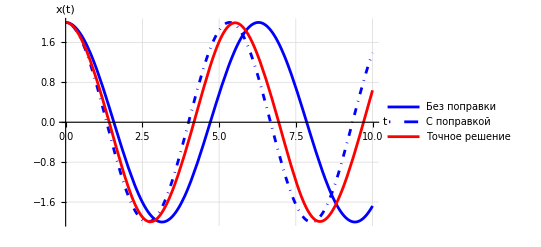

```mathematica
Plot[{nx0, nx1, nx}, {t, 0, 10}, PlotLegends -> Placed[{"Без поправки", "С поправкой", "Точное решение"}, Right], AxesLabel -> {t, x[t]}, 
	GridLines -> Automatic, PlotStyle -> {Blue, {Blue, DotDashed}, Red}, PlotRange -> All]
```